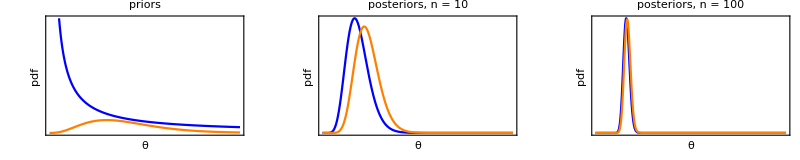

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
{α,β} = {4,2};
gPrior=Plot[{1/θ,PDF[GammaDistribution[α,β],θ]},{θ,0,20},PlotRange->{Full,{0,1}},PlotStyle->{Blue,Orange},Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"θ","pdf"},BaseStyle->{FontSize->16},PlotLabel->"priors"];
{n1,n2} = {10,100};
data1=RandomVariate[ExponentialDistribution[0.5],{n1}];
aDenom1=Integrate[(1/θ)Likelihood[ExponentialDistribution[θ],data1],{θ,0,∞}];
data2=RandomVariate[ExponentialDistribution[0.5],{n2}];
aDenom2=Integrate[(1/θ)Likelihood[ExponentialDistribution[θ],data2],{θ,0,∞}];
aPosterior[θ_,aDenom_,data__]:= (1/θ)Likelihood[ExponentialDistribution[θ],data]/aDenom
gPosterior1=Plot[{aPosterior[θ,aDenom1,data1],PDF[GammaDistribution[α+n1,1/(β+Total@data1)],θ]},{θ,0,3},PlotRange->Full,PlotStyle->{Blue,Orange},Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"θ","pdf"},BaseStyle->{FontSize->16},PlotLabel->"posteriors, n = 10"];
gPosterior2=Plot[{aPosterior[θ,aDenom2,data2],PDF[GammaDistribution[α+n2,1/(β+Total@data2)],θ]},{θ,0,3},PlotRange->Full,PlotStyle->{Blue,Orange},Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"θ","pdf"},BaseStyle->{FontSize->16},PlotLabel->"posteriors, n = 100"];
gFinal=Show[GraphicsRow[{gPrior,gPosterior1,gPosterior2}],ImageSize->800]
```

```mathematica
Export["Objective_referencePriorsExponential.pdf",gFinal]
```

Objective_referencePriorsExponential.pdf